## Geometrical Spreading code for Multilayered VTI media_direct

```mathematica
Clear["Global`*"]
```

#### layer parameters

```mathematica
eta[1]=0.1
```

0.1

```mathematica
eta[2]=0.12
```

0.12

```mathematica
eta[3]=0.18
```

0.18

```mathematica
eta[4]=0.2
```

0.2

```mathematica
eta[5]=0.22
```

0.22

```mathematica
v0[1]=1.5;
v0[2]=1.8;
v0[3]=2;
v0[4]=2.2;
v0[5]=2.5;
```

```mathematica
param={v01->1.74,v02->1.85,v03->1.94,v04->2.14,v05->2.22,v06->2,v07->1.99,v08->1.9,v09->2.2,v010->2.05,v011->2.65,v012->2.75,v013->2.64,delta1->0.1,delta2->0.12,delta3->0.25,delta4->0.15,delta5->0.2,delta6->0.1,delta7->0.05,delta8->0.04,delta9->0.06,delta10->0.1,delta11->0.07,delta12->0.1,delta13->0.04}
```

{v01→1.74,v02→1.85,v03→1.94,v04→2.14,v05→2.22,v06→2,v07→1.99,v08→1.9,v09→2.2,v010→2.05,v011→2.65,v012→2.75,v013→2.64,delta1→0.1,delta2→0.12,delta3→0.25,delta4→0.15,delta5→0.2,delta6→0.1,delta7→0.05,delta8→0.04,delta9→0.06,delta10→0.1,delta11→0.07,delta12→0.1,delta13→0.04}

```mathematica
vn[1]=1.7
vn[2]=2
vn[3]=2.3
vn[4]=2.5
vn[5]=2.8
```

1.7

2

2.3

2.5

2.8

### layer thickness

```mathematica
z0[1]=0.3;
z0[2]=0.7;
z0[3]=1;
z0[4]=1.5;
z0[5]=0.5;
```

```mathematica
T0=Sum[z0[i]/v0[i],{i,1,5}]
```

1.97071

```mathematica
VN=Sqrt[Sum[vn[i]^2*z0[i]/v0[i],{i,1,5}]/T0]
```

2.32009

```mathematica
ETA=((Sum[(1+8*eta[i])*vn[i]^4*z0[i]/v0[i],{i,1,5}]/(T0*VN^4))-1)/8
```

0.208884

#### Multilayered model effeective V0,Vn,ETA

```mathematica
Xp=Sum[(p vn[i]^2 z0[i])/(v0[i] (1-2 p^2 eta[i] vn[i]^2)^(3/2) √(1-p^2 (1+2 eta[i]) vn[i]^2)),{i,1,5}];
```

## traveltime

```mathematica
TT0=T0+(T0 (-1+√(1+((1+8 ETA) Xp^2)/(T0^2 VN^2))))/(1+8 ETA);
TT1=√(T0^2+Xp^2/VN^2-(2 ETA Xp^4)/(T0^2 VN^4 (1+((1+2 ETA) Xp^2)/(T0^2 VN^2))));
TT2=(24 T0^10 VN^10+2 (51+104 ETA) T0^8 VN^8 Xp^2+56 (3+8 ETA) T0^6 VN^6 Xp^4+4 (33+69 ETA-16 ETA^2) T0^4 VN^4 Xp^6+8 (6+5 ETA+2 ETA^2) T0^2 VN^2 Xp^8+(6+4 ETA-ETA^2) Xp^10)/(2 VN (T0^2 VN^2+Xp^2)^(3/2) (12 T0^6 VN^6+(27+104 ETA) T0^4 VN^4 Xp^2+2 (9+14 ETA) T0^2 VN^2 Xp^4+(3+5 ETA) Xp^6));
TT3=√(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) Xp^2*T0^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))));
```

```mathematica
Texact=Sum[(√(((√(((1+2 eta[i]) (-1+p^2 (1+2 eta[i]) vn[i]^2))/(-1+2 eta[i] (-1+p^2 (1+2 eta[i]) vn[i]^2)))+(p^2 (1+2 eta[i]) vn[i]^2 √(((1+2 eta[i]) (-1+2 eta[i] (-1+p^2 (1+2 eta[i]) vn[i]^2)))/(-1+p^2 (1+2 eta[i]) vn[i]^2)))/((1-2 eta[i] (-1+p^2 (1+2 eta[i]) vn[i]^2))^2))^2 z0[i]^2)/v0[i]^2)),{i,1,5}];
```

#### relative errors

```mathematica
tvt1=Abs[(Texact-TT0)]*100/Texact;
tvt2=Abs[(Texact-TT1)]*100/Texact;
tvt3=Abs[(Texact-TT2)]*100/Texact;
tvt4=Abs[(Texact-TT3)]*100/Texact;
```

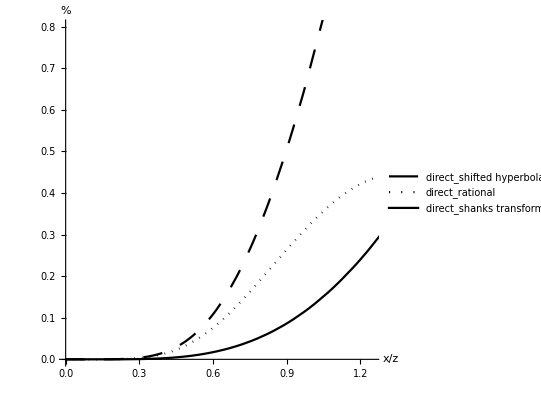

```mathematica
ParametricPlot[{{Xp/4/.param,tvt1/.param},{Xp/4/.param,tvt2/.param},{Xp/4/.param,tvt3/.param}},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Dotted,Black,Thick],Directive[Black,Thick],Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,0.8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shifted hyperbola","direct_rational","direct_shanks transform"},Right]]
```

## Shifted hyperbola

```mathematica
L00=T0 VN^2+((1+8 ETA)^2 T0 VN^2 (-1+√(1+(36 (ETA+4 ETA^2) Xp^2)/((1+8 ETA) T0^2 VN^2))))/(18 ETA (1+4 ETA));
```

## Rational

```mathematica
L11=T0 VN^2-((-1-8 ETA) Xp^2)/T0-(9 (ETA+4 ETA^2) Xp^4)/(T0^3 VN^2 (1-(9 ETA (1+4 ETA) Xp^2)/((-1-8 ETA+1/(√(1+2 ETA))) T0^2 VN^2)));
```

## Shanks transform

```mathematica
L12=(144 T0^12 VN^12+32 (15+16 ETA) T0^10 VN^10 Xp^2+2 (237+920 ETA-5152 ETA^2) T0^8 VN^8 Xp^4+8 (-3+163 ETA+2672 ETA^2) T0^6 VN^6 Xp^6-(276+847 ETA+10704 ETA^2) T0^4 VN^4 Xp^8+2 (-60-403 ETA+344 ETA^2) T0^2 VN^2 Xp^10+(-6+17 ETA-20 ETA^2) Xp^12)/(T0 (T0^2 VN^2+Xp^2) (144 T0^8 VN^8-64 (-3+10 ETA) T0^6 VN^6 Xp^2+54 (-1+32 ETA) T0^4 VN^4 Xp^4-12 (9+74 ETA) T0^2 VN^2 Xp^6+(-6+11 ETA) Xp^8));
```

```mathematica
L120=(144 T0^12 VN^12+((-6-4 ETA+ETA^2) p^12 T0^12 VN^24)/((1-2 ETA p^2 VN^2)^18 (1-(1+2 ETA) p^2 VN^2)^6)-(8 (15-3 ETA+44 ETA^2) p^10 T0^12 VN^22)/((1-2 ETA p^2 VN^2)^15 (1-(1+2 ETA) p^2 VN^2)^5)-(4 (69+605 ETA+108 ETA^2) p^8 T0^12 VN^20)/((1-2 ETA p^2 VN^2)^12 (1-(1+2 ETA) p^2 VN^2)^4)-(8 (3+296 ETA+880 ETA^2) p^6 T0^12 VN^18)/((1-2 ETA p^2 VN^2)^9 (1-(1+2 ETA) p^2 VN^2)^3)+(2 (237+1320 ETA+3040 ETA^2) p^4 T0^12 VN^16)/((1-2 ETA p^2 VN^2)^6 (1-(1+2 ETA) p^2 VN^2)^2)+(160 (3+16 ETA) p^2 T0^12 VN^14)/((1-2 ETA p^2 VN^2)^3 (1-(1+2 ETA) p^2 VN^2)))/(2 T0 (T0^2 VN^2+(p^2 T0^2 VN^4)/((1-2 ETA p^2 VN^2)^3 (1-(1+2 ETA) p^2 VN^2))) (72 T0^8 VN^8-((3+5 ETA) p^8 T0^8 VN^16)/((1-2 ETA p^2 VN^2)^12 (1-(1+2 ETA) p^2 VN^2)^4)-(2 (27+4 ETA) p^6 T0^8 VN^14)/((1-2 ETA p^2 VN^2)^9 (1-(1+2 ETA) p^2 VN^2)^3)-((27+784 ETA) p^4 T0^8 VN^12)/((1-2 ETA p^2 VN^2)^6 (1-(1+2 ETA) p^2 VN^2)^2)+(32 (3+22 ETA) p^2 T0^8 VN^10)/((1-2 ETA p^2 VN^2)^3 (1-(1+2 ETA) p^2 VN^2))));
```

## GMA

```mathematica
L22=T0 VN^2-((-1-8 ETA) Xp^2)/T0-(18 (ETA+4 ETA^2) Xp^4)/(T0^3 VN^2 (1+(((-1-8 ETA)^2/T0^2+(2 (-1-8 ETA) √(1/(1+2 ETA)))/T0^2+1/((1+2 ETA) T0^2)+(18 (ETA+4 ETA^2))/T0^2-(18 (1+6 ETA) (ETA+4 ETA^2))/((1/(1+2 ETA))^(3/2) T0^2)) Xp^2)/((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0) (T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2)))+√(1+(2 ((-1-8 ETA)^2/T0^2+(2 (-1-8 ETA) √(1/(1+2 ETA)))/T0^2+1/((1+2 ETA) T0^2)+(18 (ETA+4 ETA^2))/T0^2-(18 (1+6 ETA) (ETA+4 ETA^2))/((1/(1+2 ETA))^(3/2) T0^2)) Xp^2)/((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0) (T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2)))+((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0)^2 Xp^4)/((T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2))^2))));
```

## exact

```mathematica
L33=Sqrt[(Xp/p)*D[Xp,p]];
```

#### relative errors

```mathematica
pp1=Abs[(L33-L00)]*100/L33;
pp2=Abs[(L33-L11)]*100/L33;
pp22=Abs[(L33-L120)]*100/L33;
pp3=Abs[(L33-L22)]*100/L33;
```

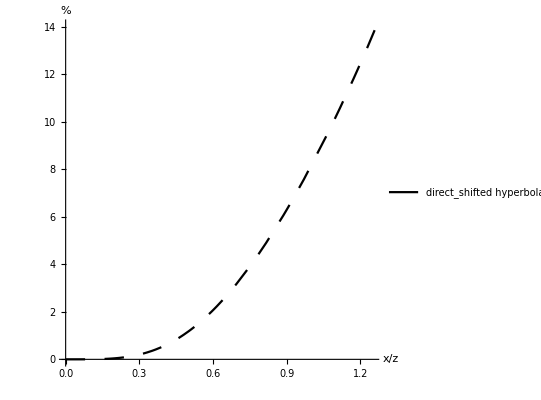
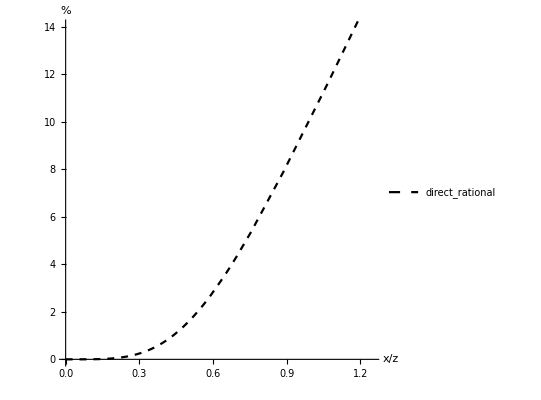
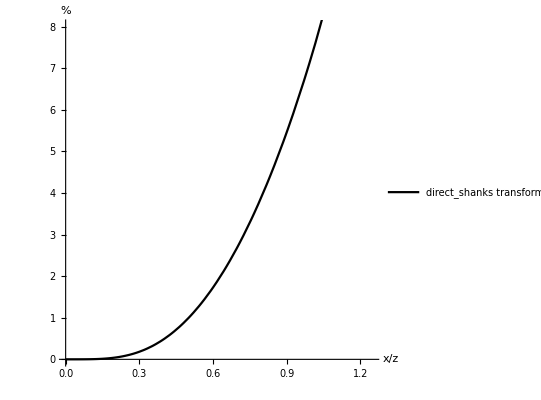

```mathematica
{a00=ParametricPlot[{Xp/4/.param,pp1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,14}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shifted hyperbola"},Right]],
a01=ParametricPlot[{Xp/4/.param,pp2/.param},{p,0,0.9},PlotStyle->{Dashing[Small],Black,Thick},AspectRatio->1,PlotRange->{{0,1.25},{0,14}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_rational"},Right]],a012=ParametricPlot[{Xp/4/.param,pp22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shanks transform"},Right]]}
```

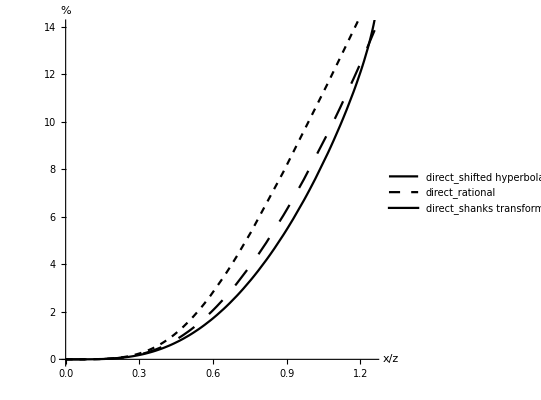

```mathematica
Show[a00,a01,a012]
```

## indirect approximations

### shifted hyperbola

```mathematica
LL00=(T0^2 VN^2+Xp^2+8 ETA Xp^2)/T0;
```

### rational

```mathematica
LL11=1/(√((T0^2 (T0^12 VN^12+2 (3-2 ETA) T0^10 VN^10 Xp^2-3 (-5+2 ETA+4 ETA^2) T0^8 VN^8 Xp^4-4 (-5-4 ETA+4 ETA^2) T0^6 VN^6 Xp^6+(15+44 ETA+36 ETA^2-16 ETA^3) T0^4 VN^4 Xp^8+6 (1+2 ETA)^3 T0^2 VN^2 Xp^10+(1+2 ETA)^2 (1+6 ETA+4 ETA^2) Xp^12))/((T0^2 VN^2+(1+2 ETA) Xp^2)^4 (T0^4 VN^4+2 (1+ETA) T0^2 VN^2 Xp^2+Xp^4)^2)));
```

### shanks transfrom

```mathematica
LL12=2/(√((T0^2 (995328 T0^38 VN^38+82944 (183+328 ETA) T0^36 VN^36 Xp^2+13824 (7857+26280 ETA+23168 ETA^2) T0^34 VN^34 Xp^4+1152 (420471+1961712 ETA+3133056 ETA^2+1254400 ETA^3) T0^32 VN^32 Xp^6-48 (-31416741-181092672 ETA-390049920 ETA^2-286679040 ETA^3+74629120 ETA^4) T0^30 VN^30 Xp^8+4 (869728347+5785761960 ETA+14817513600 ETA^2+14894392320 ETA^3-3644375040 ETA^4-13084524544 ETA^5) T0^28 VN^28 Xp^10-8 (-770109039-5655435714 ETA-16005265200 ETA^2-19394737920 ETA^3+139180032 ETA^4+23512711168 ETA^5+9214885888 ETA^6) T0^26 VN^26 Xp^12+4 (2140105617+16809205455 ETA+50013763848 ETA^2+67734901440 ETA^3+25965364224 ETA^4-40496521216 ETA^5-35840589824 ETA^6+55289315328 ETA^7) T0^24 VN^24 Xp^14+16 (591137352+4849583319 ETA+14621211612 ETA^2+20915135280 ETA^3+17626175280 ETA^4+14122674176 ETA^5+2704293888 ETA^6-10100932608 ETA^7) T0^22 VN^22 Xp^16+4 (2092689027+17609825574 ETA+52317840600 ETA^2+75079254960 ETA^3+95584354992 ETA^4+150594974848 ETA^5+82994176000 ETA^6-88153128960 ETA^7) T0^20 VN^20 Xp^18+8 (743663349+6332087520 ETA+18174548880 ETA^2+24724456020 ETA^3+38682228720 ETA^4+70287173344 ETA^5+45450745856 ETA^6-10110074880 ETA^7) T0^18 VN^18 Xp^20+12 (282480939+2410875819 ETA+6615843840 ETA^2+7936132410 ETA^3+12605610888 ETA^4+23009138416 ETA^5+14715944448 ETA^6+7839817728 ETA^7) T0^16 VN^16 Xp^22+12 (128268036+1091637000 ETA+2868302304 ETA^2+2745170160 ETA^3+3160029537 ETA^4+5741904272 ETA^5+2210544128 ETA^6+4429074432 ETA^7) T0^14 VN^14 Xp^24+3 (183701196+1558202832 ETA+3982591296 ETA^2+2660529120 ETA^3-461463787 ETA^4+488594632 ETA^5-3113577856 ETA^6+514013184 ETA^7) T0^12 VN^12 Xp^26-2 (-76518756-649768392 ETA-1664521920 ETA^2-690888960 ETA^3+2275819137 ETA^4+2457497534 ETA^5+2193186528 ETA^6+2020520448 ETA^7) T0^10 VN^10 Xp^28+(32154732+275887620 ETA+736676640 ETA^2+231788880 ETA^3-1612455255 ETA^4-1793900921 ETA^5-584805536 ETA^6-607527936 ETA^7) T0^8 VN^8 Xp^30+4 (1230552+10809612 ETA+31313520 ETA^2+14462640 ETA^3-69711072 ETA^4-86098075 ETA^5-4745771 ETA^6+12262560 ETA^7) T0^6 VN^6 Xp^32+(516132+4714200 ETA+15307488 ETA^2+13448160 ETA^3-20654847 ETA^4-36620206 ETA^5-4192743 ETA^6+9583656 ETA^7) T0^4 VN^4 Xp^34-2 (3+5 ETA)^2 (-1836-11592 ETA-22116 ETA^2+6160 ETA^3+15217 ETA^4+642 ETA^5) T0^2 VN^2 Xp^36-(3+5 ETA)^2 (-108-756 ETA-1980 ETA^2-2300 ETA^3-667 ETA^4+231 ETA^5) Xp^38))/((T0^2 VN^2+Xp^2)^6 (12 T0^6 VN^6+(27+104 ETA) T0^4 VN^4 Xp^2+2 (9+14 ETA) T0^2 VN^2 Xp^4+(3+5 ETA) Xp^6)^5)));
```

### GMA

```mathematica
LL22=((√2)/(√((((2 Xp)/VN^2+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))) (-(((2 Xp)/VN^2+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))^2)/(4 (T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))^(3/2))+(2/VN^2-(8 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))^2)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^3)+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2))/((1+2 ETA) VN^2)-(((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))^2)/(4 (T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))^(3/2))+((4 (1+8 ETA+8 ETA^2) T0^2)/((1+2 ETA) VN^2)+(12 Xp^2)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)+(32 ETA Xp^3 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(48 ETA Xp^2)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(2 √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))))))/(Xp √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))))));
```

```mathematica
bb1=Abs[(L33-LL00)]*100/L33;
bb2=Abs[(L33-LL11)]*100/L33;
bb22=Abs[(L33-LL12)]*100/L33;
bb3=Abs[(L33-LL22)]*100/L33;
```

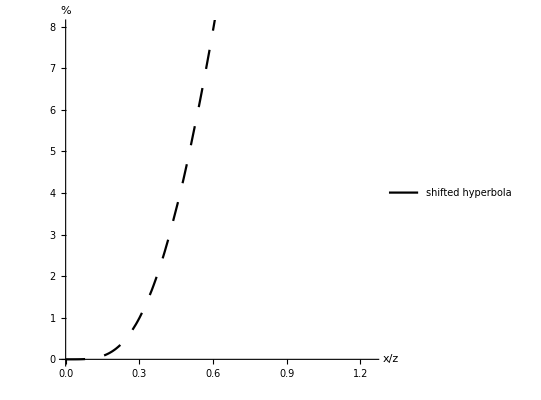
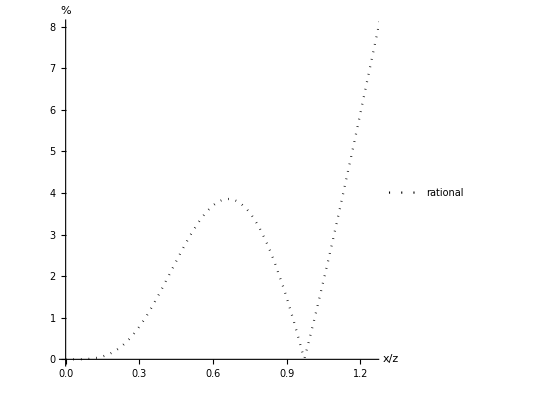
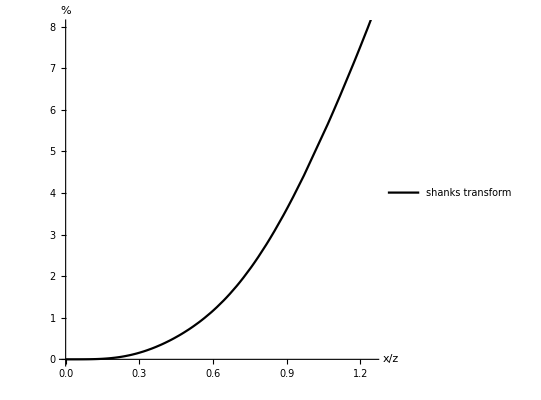

```mathematica
{b00=ParametricPlot[{Xp/4/.param,bb1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shifted hyperbola"},Right]],
b01=ParametricPlot[{Xp/4/.param,bb2/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"rational"},Right]],b012=ParametricPlot[{Xp/4/.param,bb22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shanks transform"},Right]]}
```

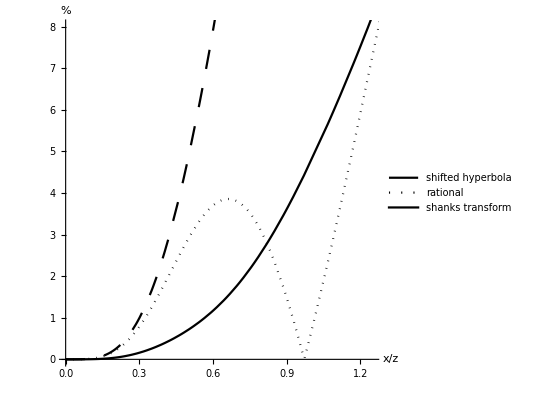

```mathematica
Show[b00,b01,b012]
```

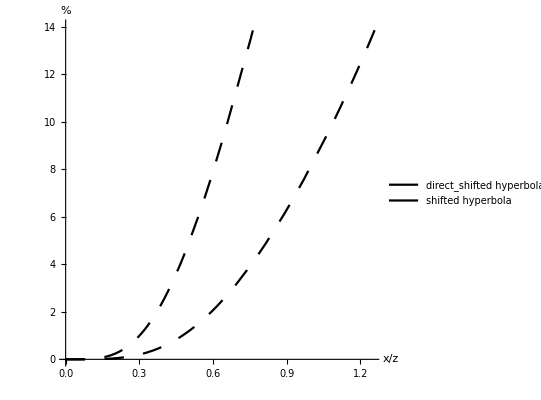
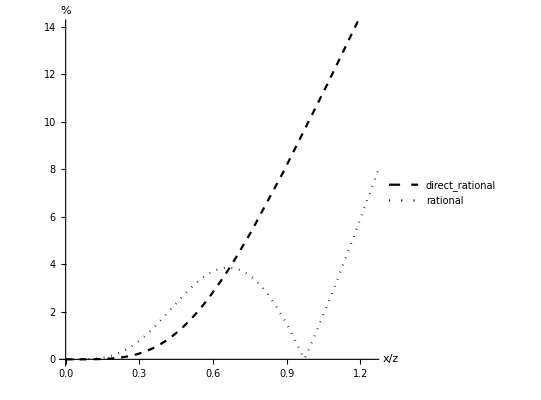
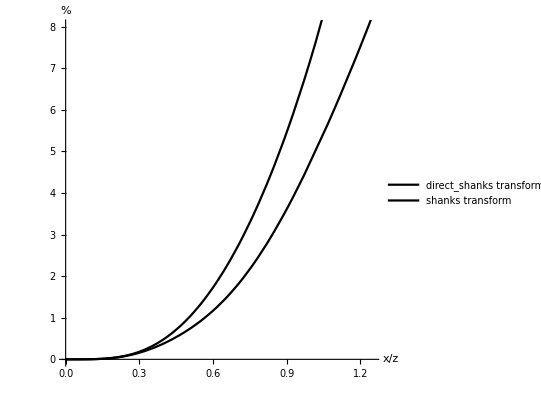

```mathematica
{Show[a00,b00],Show[a01,b01],Show[a012,b012]}
```

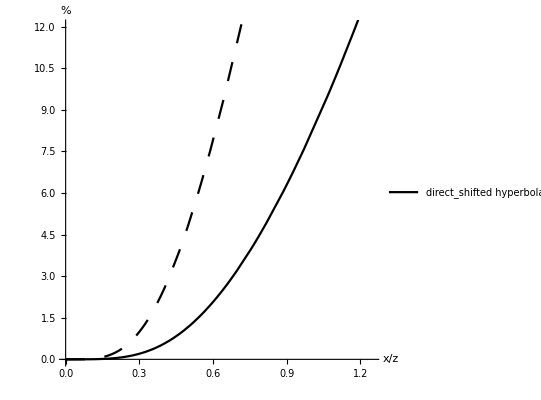
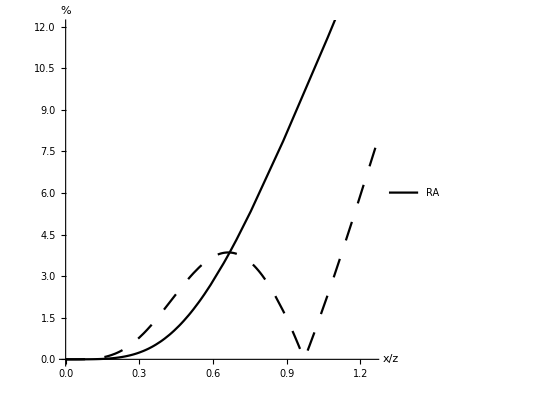
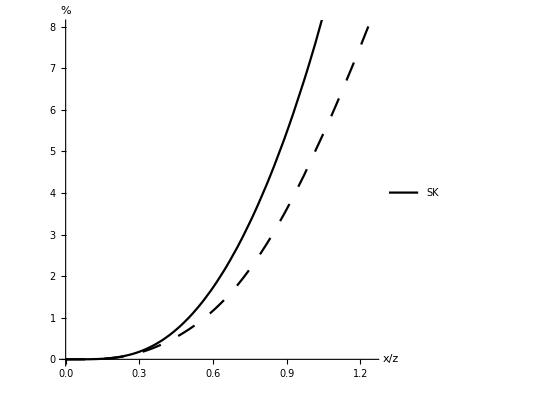

```mathematica
{ParametricPlot[{{Xp/4/.param,bb1/.param},{Xp/4/.param,pp1/.param}},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,12}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shifted hyperbola"},Right]],ParametricPlot[{{Xp/4/.param,bb2/.param},{Xp/4/.param,pp2/.param}},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,12}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"RA"},Right]],ParametricPlot[{{Xp/4/.param,bb22/.param},{Xp/4/.param,pp22/.param}},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick],Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,8}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"SK"},Right]]}
```